```mathematica
m={{-m1*ω^2+k1+k2,-k1-k2*ExpToTrig[Exp[I*q*a]]},{-k1-k2*ExpToTrig[Exp[-I*q*a]],-m2*ω^2+k1+k2}};
```

```mathematica
determinante=Det[m]/.ω^2->z/.ω^4->z^2
```

2 k1 k2+k2^2-k1 m1 z-k2 m1 z-k1 m2 z-k2 m2 z+m1 m2 z^2-2 k1 k2 Cos[a q]-k2^2 Cos[a q]^2-k2^2 Sin[a q]^2

```mathematica
solucion=Solve[determinante==0,z]
```

{{z→1/(2 m1 m2)(k1 m1+k2 m1+k1 m2+k2 m2-√((-k1 m1-k2 m1-k1 m2-k2 m2)^2-4 m1 m2 (2 k1 k2+k2^2-2 k1 k2 Cos[a q]-k2^2 Cos[a q]^2-k2^2 Sin[a q]^2)))},{z→1/(2 m1 m2)(k1 m1+k2 m1+k1 m2+k2 m2+√((-k1 m1-k2 m1-k1 m2-k2 m2)^2-4 m1 m2 (2 k1 k2+k2^2-2 k1 k2 Cos[a q]-k2^2 Cos[a q]^2-k2^2 Sin[a q]^2)))}}

```mathematica
final1=z/.solucion[[1]];
final2=z/.solucion[[2]];
```

```mathematica
Simplify[final1]
```

(k1 m1+k2 m1+k1 m2+k2 m2-√((k1+k2)^2 (m1+m2)^2+8 k1 k2 m1 m2 (-1+Cos[a q])))/(2 m1 m2)

```mathematica
grafica1=final1/.m1->2/.m2->1/.k1->2/.a->1/.k2->2;
grafica2=final2/.m1->2/.m2->1/.k1->2/.a->1/.k2->2;
rango1=-Pi/a/.a->1;
rango2=Pi/a/.a->1;
g1=Plot[{Sqrt[grafica1/.(a*q)->r],Sqrt[grafica2/.(a*q)->r]},{r,rango1,rango2},PlotRange->{0,2.5},PlotStyle->{Black,{Black,Dashed}},LabelStyle->Medium,AxesLabel->{"q","ω(q)"}]
```

-Graphics-

```mathematica
ωmenos[m1_,m2_,k1_,k2_,y_]:=Sqrt[(k1 m1+k2 m1+k1 m2+k2 m2-√((k1+k2)^2 (m1+m2)^2+8 k1 k2 m1 m2 (-1+Cos[y])))/(2 m1 m2)];
ωmas[m1_,m2_,k1_,k2_,y_]:=Sqrt[(k1 m1+k2 m1+k1 m2+k2 m2+√((k1+k2)^2 (m1+m2)^2+8 k1 k2 m1 m2 (-1+Cos[y])))/(2 m1 m2)]
```

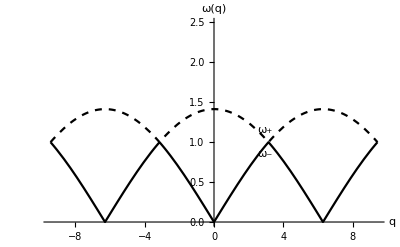

```mathematica
m1=2;
m2=4m1/4;
k1=1;
k2=k1;
text1=Graphics[Text[SubMinus[ω],{Pi-0.2,ωmenos[m1,m2,k1,k2,Pi-0.2]-0.1}]];
text2=Graphics[Text[SubPlus[ω],{Pi-0.2,ωmas[m1,m2,k1,k2,Pi-0.2]+0.1}]];
g1=Plot[{ωmenos[m1,m2,k1,k2,y],ωmas[m1,m2,k1,k2,y]},{y,-3Pi,3Pi},PlotRange->{0,2.5},PlotStyle->{Black,{Black,Dashed}},LabelStyle->Medium,AxesLabel->{"q","ω(q)"}];
final=Show[g1,text1,text2]
```

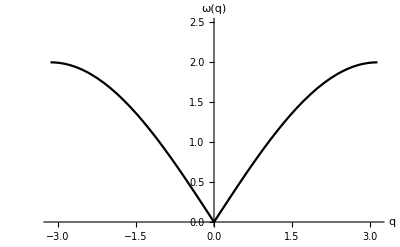

```mathematica
k=1;
m=1;
a=1;
final=Plot[2Sqrt[k/m]Abs[Sin[q*a/2]],{q,-Pi,Pi},PlotRange->{0,2.5},PlotStyle->{Black},LabelStyle->Medium,AxesLabel->{"q","ω(q)"}]
```

```mathematica
Export["Figura_1_part_cristal_1D.png",final]
```

Figura_1_part_cristal_1D.png

```mathematica
?PlotLabel
```